```mathematica
DataDir = "/Users/haeun/OneDrive - University of North Carolina at Chapel Hill/Rotation3_Palmer/Work/data/NSCLC/";
FilePrefix = "NSNSCLC_atezo_chemo_Socinski2018";
```

```mathematica
DigitizeItData=Import[DataDir<>FilePrefix <> ".csv","CSV"];
DigitizeItData//Dimensions
```

{5886,2}

```mathematica
(* Convert scale to 0-1 *)
DigitizeItData⟦2;;,2⟧ = DigitizeItData⟦2;;,2⟧  / 100;
```

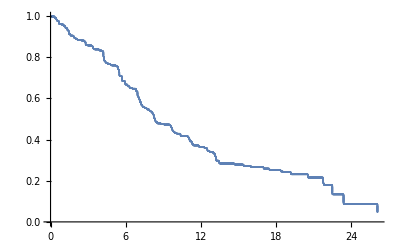

```mathematica
ListPlot[DigitizeItData⟦2;;⟧]
```

```mathematica
IPDdata=Import[DataDir<>FilePrefix <> "_indiv.csv","CSV"];
IPDdata//Dimensions
IPDdataTimes=IPDdata⟦2;;,1⟧
IPDdataCensoring=1-IPDdata⟦2;;,2⟧
```

{357,5}

{0.0361,0.0361,0.0361,0.0361,0.0361,0.47,0.497,0.527,0.65,0.662,0.665,0.665,0.673,0.801,1.03,1.05,1.07,1.17,1.19,1.2,1.23,1.34,1.35,1.36,1.44,1.46,1.46,1.46,1.47,1.47,1.57,1.59,1.6,1.83,1.85,1.87,1.9,2.01,2.04,2.15,2.45,2.68,2.72,2.78,2.8,2.8,2.81,2.81,2.83,3,3.31,3.38,3.39,3.4,3.42,3.48,3.87,3.9,4.09,4.2,4.22,4.22,4.22,4.22,4.23,4.23,4.23,4.23,4.25,4.27,4.27,4.27,4.28,4.28,4.29,4.32,4.37,4.4,4.44,4.57,4.6,4.8,4.84,5.22,5.28,5.38,5.39,5.4,5.4,5.42,5.46,5.47,5.48,5.49,5.49,5.5,5.5,5.5,5.51,5.51,5.53,5.68,5.69,5.7,5.7,5.71,5.72,5.73,5.73,5.93,5.95,5.96,5.96,5.97,5.98,6.13,6.15,6.16,6.3,6.34,6.34,6.51,6.82,6.83,6.84,6.84,6.87,6.95,6.95,6.95,6.95,6.96,6.96,6.96,6.97,7.01,7.04,7.07,7.09,7.1,7.11,7.13,7.13,7.14,7.16,7.24,7.24,7.25,7.25,7.31,7.34,7.35,7.47,7.51,7.55,7.69,7.72,7.88,7.91,7.94,8.06,8.09,8.14,8.17,8.2,8.23,8.24,8.25,8.25,8.26,8.27,8.31,8.33,8.34,8.35,8.38,8.4,8.49,8.52,8.53,8.83,9.09,9.56,9.6,9.63,9.66,9.68,9.71,9.72,9.74,9.77,9.83,9.91,9.93,10.2,10.4,10.4,10.5,11,11.1,11.1,11.1,11.1,11.2,11.2,11.3,11.4,11.4,11.4,11.5,11.9,12,12.4,12.5,12.6,12.6,12.7,13,13.1,13.1,13.2,13.2,13.2,13.2,13.3,13.3,13.3,13.5,13.5,13.6,14.8,15.5,16.1,17.1,17.6,18.6,19.3,20.6,21.9,22.6,23.5,0.0936,0.1855,0.2745,0.366,0.4595,0.5495,0.642,0.733,0.8245,0.9205,6.495,8.075,8.145,8.215,8.28,8.355,8.425,8.495,8.575,8.645,8.715,8.785,8.855,8.925,9.065,9.135,9.195,9.265,9.335,9.395,9.465,9.535,9.595,9.665,9.735,9.795,9.865,9.935,10.05,10.15,10.25,10.35,10.45,10.55,10.65,10.75,10.85,11.05,11.15,11.25,11.35,11.45,11.45,11.55,11.65,11.75,11.85,11.95,12.15,12.35,12.55,12.75,13.15,13.25,13.45,13.55,13.75,13.85,14.35,14.65,15.05,15.15,15.25,15.35,15.35,15.45,15.55,15.65,15.65,15.75,15.85,15.95,16.35,16.65,17.05,17.15,17.25,17.35,17.45,17.55,17.65,17.75,17.85,17.95,18.35,18.65,19.15,19.25,19.35,19.45,19.65,19.75,19.85,20.25,20.45,20.75,21.15,21.25,21.35,21.45,21.65,21.75,21.85,26,26}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
IPDdata⟦1;;10⟧//TableForm
```

Time | Event | Arm | Subpop | Slide
0.0361 | 1 | NA | NA | NA
0.0361 | 1 | NA | NA | NA
0.0361 | 1 | NA | NA | NA
0.0361 | 1 | NA | NA | NA
0.0361 | 1 | NA | NA | NA
0.47 | 1 | NA | NA | NA
0.497 | 1 | NA | NA | NA
0.527 | 1 | NA | NA | NA
0.65 | 1 | NA | NA | NA

```mathematica
MaximumTime=Max[Max[IPDdataTimes],Max[DigitizeItData⟦2;;,1⟧]]
```

26.1148

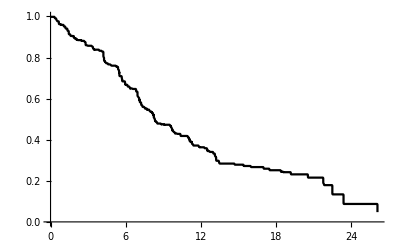

```mathematica
DigitizeItPlot=ListPlot[DigitizeItData⟦2;;⟧,Joined->True,PlotRange->{{0,MaximumTime},{0,1}},PlotStyle->Black]
```

```mathematica
IPDdataTimes
```

{0.0361,0.0361,0.0361,0.0361,0.0361,0.47,0.497,0.527,0.65,0.662,0.665,0.665,0.673,0.801,1.03,1.05,1.07,1.17,1.19,1.2,1.23,1.34,1.35,1.36,1.44,1.46,1.46,1.46,1.47,1.47,1.57,1.59,1.6,1.83,1.85,1.87,1.9,2.01,2.04,2.15,2.45,2.68,2.72,2.78,2.8,2.8,2.81,2.81,2.83,3,3.31,3.38,3.39,3.4,3.42,3.48,3.87,3.9,4.09,4.2,4.22,4.22,4.22,4.22,4.23,4.23,4.23,4.23,4.25,4.27,4.27,4.27,4.28,4.28,4.29,4.32,4.37,4.4,4.44,4.57,4.6,4.8,4.84,5.22,5.28,5.38,5.39,5.4,5.4,5.42,5.46,5.47,5.48,5.49,5.49,5.5,5.5,5.5,5.51,5.51,5.53,5.68,5.69,5.7,5.7,5.71,5.72,5.73,5.73,5.93,5.95,5.96,5.96,5.97,5.98,6.13,6.15,6.16,6.3,6.34,6.34,6.51,6.82,6.83,6.84,6.84,6.87,6.95,6.95,6.95,6.95,6.96,6.96,6.96,6.97,7.01,7.04,7.07,7.09,7.1,7.11,7.13,7.13,7.14,7.16,7.24,7.24,7.25,7.25,7.31,7.34,7.35,7.47,7.51,7.55,7.69,7.72,7.88,7.91,7.94,8.06,8.09,8.14,8.17,8.2,8.23,8.24,8.25,8.25,8.26,8.27,8.31,8.33,8.34,8.35,8.38,8.4,8.49,8.52,8.53,8.83,9.09,9.56,9.6,9.63,9.66,9.68,9.71,9.72,9.74,9.77,9.83,9.91,9.93,10.2,10.4,10.4,10.5,11,11.1,11.1,11.1,11.1,11.2,11.2,11.3,11.4,11.4,11.4,11.5,11.9,12,12.4,12.5,12.6,12.6,12.7,13,13.1,13.1,13.2,13.2,13.2,13.2,13.3,13.3,13.3,13.5,13.5,13.6,14.8,15.5,16.1,17.1,17.6,18.6,19.3,20.6,21.9,22.6,23.5,0.0936,0.1855,0.2745,0.366,0.4595,0.5495,0.642,0.733,0.8245,0.9205,6.495,8.075,8.145,8.215,8.28,8.355,8.425,8.495,8.575,8.645,8.715,8.785,8.855,8.925,9.065,9.135,9.195,9.265,9.335,9.395,9.465,9.535,9.595,9.665,9.735,9.795,9.865,9.935,10.05,10.15,10.25,10.35,10.45,10.55,10.65,10.75,10.85,11.05,11.15,11.25,11.35,11.45,11.45,11.55,11.65,11.75,11.85,11.95,12.15,12.35,12.55,12.75,13.15,13.25,13.45,13.55,13.75,13.85,14.35,14.65,15.05,15.15,15.25,15.35,15.35,15.45,15.55,15.65,15.65,15.75,15.85,15.95,16.35,16.65,17.05,17.15,17.25,17.35,17.45,17.55,17.65,17.75,17.85,17.95,18.35,18.65,19.15,19.25,19.35,19.45,19.65,19.75,19.85,20.25,20.45,20.75,21.15,21.25,21.35,21.45,21.65,21.75,21.85,26,26}

```mathematica
IPDdataCensoring
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
MyEventData=EventData[IPDdataTimes,IPDdataCensoring]
```

EventData[…]

```mathematica
MySurvivalModel=SurvivalModelFit[MyEventData]
```

SurvivalModel[…]

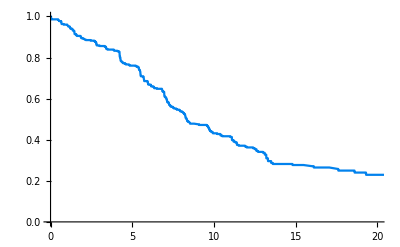

```mathematica
IPDPlot=Plot[MySurvivalModel[t],{t,0,MaximumTime},PlotRange->{{0,20},{0,1}},PlotStyle->ColorData[3,6],Exclusions->None, ImageSize-> {{10*72}, {10 * 72}}]
```

```mathematica
Export[DataDir <> FilePrefix <> ".png", IPDPlot, "PNG"]
```

/Users/haeun/OneDrive - University of North Carolina at Chapel Hill/Rotation3_Palmer/Work/data/NSCLC/NSNSCLC_atezo_chemo_Socinski2018.png

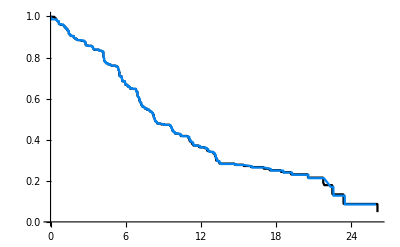

```mathematica
Show[DigitizeItPlot,IPDPlot]
```

```mathematica
Prediction[t_]:=Max[0.0006622516556291391 Boole[0.011>t]+0.0006622516556291391 Boole[0.022>t]+0.0006622516556291391 Boole[0.044>t]+0.0013245033112582781 Boole[0.055>t]+0.0006622516556291391 Boole[0.066>t]+0.0026490066225165563 Boole[0.186>t]+0.0006622516556291391 Boole[0.197>t]+0.0006622516556291391 Boole[0.20800000000000002>t]+0.0006622516556291391 Boole[0.273>t]+0.0006622516556291391 Boole[0.306>t]+0.0006622516556291391 Boole[0.339>t]+0.0006622516556291391 Boole[0.371>t]+0.0006622516556291391 Boole[0.382>t]+0.0006622516556291391 Boole[0.393>t]+0.0006622516556291391 Boole[0.71>t]+0.0006622516556291391 Boole[0.732>t]+0.0006622516556291391 Boole[0.754>t]+0.0006622516556291391 Boole[0.765>t]+0.0006622516556291391 Boole[0.776>t]+0.0006622516556291391 Boole[0.787>t]+0.006622516556291391 Boole[0.808>t]+0.0013245033112582781 Boole[0.8190000000000001>t]+0.0013245033112582781 Boole[0.8300000000000001>t]+0.005298013245033113 Boole[0.841>t]+0.004635761589403974 Boole[0.852>t]+0.0006622516556291391 Boole[0.863>t]+0.0006622516556291391 Boole[0.874>t]+0.001986754966887417 Boole[0.907>t]+0.0013245033112582781 Boole[0.918>t]+0.001986754966887417 Boole[0.9400000000000001>t]+0.0006622516556291391 Boole[0.9500000000000001>t]+0.0006622516556291391 Boole[0.961>t]+0.001986754966887417 Boole[0.983>t]+0.001986754966887417 Boole[0.994>t]+0.001986754966887417 Boole[1.0050000000000001>t]+0.0026490066225165563 Boole[1.016>t]+0.001986754966887417 Boole[1.027>t]+0.0013245033112582781 Boole[1.038>t]+0.0006622516556291391 Boole[1.049>t]+0.0006622516556291391 Boole[1.06>t]+0.0013245033112582781 Boole[1.147>t]+0.0006622516556291391 Boole[1.169>t]+0.0013245033112582781 Boole[1.18>t]+0.0013245033112582781 Boole[1.191>t]+0.0013245033112582781 Boole[1.202>t]+0.005298013245033113 Boole[1.213>t]+0.0033112582781456954 Boole[1.235>t]+0.0013245033112582781 Boole[1.245>t]+0.0006622516556291391 Boole[1.2670000000000001>t]+0.001986754966887417 Boole[1.344>t]+0.0033112582781456954 Boole[1.355>t]+0.009271523178807948 Boole[1.366>t]+0.0006622516556291391 Boole[1.377>t]+0.0033112582781456954 Boole[1.3980000000000001>t]+0.0013245033112582781 Boole[1.409>t]+0.0006622516556291391 Boole[1.442>t]+0.0013245033112582781 Boole[1.486>t]+0.0013245033112582781 Boole[1.497>t]+0.0013245033112582781 Boole[1.508>t]+0.001986754966887417 Boole[1.5190000000000001>t]+0.0013245033112582781 Boole[1.5290000000000001>t]+0.008609271523178808 Boole[1.562>t]+0.0006622516556291391 Boole[1.573>t]+0.0006622516556291391 Boole[1.584>t]+0.001986754966887417 Boole[1.595>t]+0.007947019867549669 Boole[1.606>t]+0.0006622516556291391 Boole[1.617>t]+0.001986754966887417 Boole[1.6280000000000001>t]+0.0013245033112582781 Boole[1.639>t]+0.0006622516556291391 Boole[1.661>t]+0.0013245033112582781 Boole[1.693>t]+0.0013245033112582781 Boole[1.704>t]+0.0013245033112582781 Boole[1.726>t]+0.001986754966887417 Boole[1.737>t]+0.0013245033112582781 Boole[1.748>t]+0.00728476821192053 Boole[1.7590000000000001>t]+0.0006622516556291391 Boole[1.77>t]+0.0006622516556291391 Boole[1.7810000000000001>t]+0.001986754966887417 Boole[1.792>t]+0.001986754966887417 Boole[1.803>t]+0.0006622516556291391 Boole[1.835>t]+0.018543046357615896 Boole[1.857>t]+0.0006622516556291391 Boole[1.868>t]+0.0006622516556291391 Boole[1.879>t]+0.0013245033112582781 Boole[1.901>t]+0.0006622516556291391 Boole[1.923>t]+0.0006622516556291391 Boole[1.956>t]+0.0006622516556291391 Boole[1.966>t]+0.0006622516556291391 Boole[1.977>t]+0.0006622516556291391 Boole[1.999>t]+0.0006622516556291391 Boole[2.0100000000000002>t]+0.008609271523178808 Boole[2.021>t]+0.0013245033112582781 Boole[2.032>t]+0.0013245033112582781 Boole[2.054>t]+0.0013245033112582781 Boole[2.065>t]+0.001986754966887417 Boole[2.076>t]+0.0013245033112582781 Boole[2.087>t]+0.001986754966887417 Boole[2.098>t]+0.001986754966887417 Boole[2.109>t]+0.0013245033112582781 Boole[2.119>t]+0.001986754966887417 Boole[2.13>t]+0.001986754966887417 Boole[2.141>t]+0.0013245033112582781 Boole[2.152>t]+0.001986754966887417 Boole[2.1630000000000003>t]+0.001986754966887417 Boole[2.174>t]+0.0013245033112582781 Boole[2.185>t]+0.001986754966887417 Boole[2.196>t]+0.001986754966887417 Boole[2.207>t]+0.0013245033112582781 Boole[2.218>t]+0.001986754966887417 Boole[2.229>t]+0.0013245033112582781 Boole[2.24>t]+0.001986754966887417 Boole[2.251>t]+0.001986754966887417 Boole[2.261>t]+0.017218543046357615 Boole[2.2720000000000002>t]+0.013245033112582781 Boole[2.283>t]+0.0006622516556291391 Boole[2.294>t]+0.0006622516556291391 Boole[2.305>t]+0.007947019867549669 Boole[2.316>t]+0.0013245033112582781 Boole[2.327>t]+0.006622516556291391 Boole[2.349>t]+0.0033112582781456954 Boole[2.371>t]+0.017218543046357615 Boole[2.382>t]+0.005298013245033113 Boole[2.3930000000000002>t]+0.005298013245033113 Boole[2.403>t]+0.016556291390728478 Boole[2.414>t]+0.004635761589403974 Boole[2.4250000000000003>t]+0.001986754966887417 Boole[2.436>t]+0.03245033112582781 Boole[2.447>t]+0.02052980132450331 Boole[2.458>t]+0.004635761589403974 Boole[2.469>t]+0.054304635761589407 Boole[2.48>t]+0.031788079470198675 Boole[2.491>t]+0.0033112582781456954 Boole[2.5020000000000002>t]+0.03443708609271523 Boole[2.513>t]+0.009933774834437087 Boole[2.524>t]+0.0013245033112582781 Boole[2.535>t]+0.0026490066225165563 Boole[2.5460000000000003>t]+0.01390728476821192 Boole[2.556>t]+0.0006622516556291391 Boole[2.567>t]+0.015894039735099338 Boole[2.578>t]+0.012582781456953643 Boole[2.589>t]+0.001986754966887417 Boole[2.6>t]+0.017880794701986755 Boole[2.611>t]+0.0026490066225165563 Boole[2.622>t]+0.0026490066225165563 Boole[2.633>t]+0.009271523178807948 Boole[2.644>t]+0.001986754966887417 Boole[2.6550000000000002>t]+0.0013245033112582781 Boole[2.666>t]+0.005960264900662251 Boole[2.677>t]+0.001986754966887417 Boole[2.688>t]+0.001986754966887417 Boole[2.698>t]+0.0026490066225165563 Boole[2.709>t]+0.00728476821192053 Boole[2.72>t]+0.0006622516556291391 Boole[2.742>t]+0.007947019867549669 Boole[2.753>t]+0.0026490066225165563 Boole[2.7640000000000002>t]+0.006622516556291391 Boole[2.775>t]+0.0033112582781456954 Boole[2.786>t]+0.0006622516556291391 Boole[2.8080000000000003>t]+0.0026490066225165563 Boole[2.84>t]+0.0006622516556291391 Boole[2.851>t]+0.0006622516556291391 Boole[2.873>t]+0.0006622516556291391 Boole[2.884>t]+0.0006622516556291391 Boole[2.895>t]+0.001986754966887417 Boole[2.906>t]+0.001986754966887417 Boole[2.9170000000000003>t]+0.005960264900662251 Boole[2.928>t]+0.0006622516556291391 Boole[2.939>t]+0.0006622516556291391 Boole[2.95>t]+0.0026490066225165563 Boole[3.0700000000000003>t]+0.0006622516556291391 Boole[3.081>t]+0.0006622516556291391 Boole[3.103>t]+0.0006622516556291391 Boole[3.1790000000000003>t]+0.0006622516556291391 Boole[3.201>t]+0.0006622516556291391 Boole[3.223>t]+0.0013245033112582781 Boole[3.234>t]+0.0006622516556291391 Boole[3.245>t]+0.0006622516556291391 Boole[3.267>t]+0.001986754966887417 Boole[3.365>t]+0.0013245033112582781 Boole[3.376>t]+0.007947019867549669 Boole[3.398>t]+0.004635761589403974 Boole[3.4090000000000003>t]+0.0006622516556291391 Boole[3.4410000000000003>t]+0.006622516556291391 Boole[3.474>t]+0.0006622516556291391 Boole[3.485>t]+0.0006622516556291391 Boole[3.6710000000000003>t]+0.0033112582781456954 Boole[3.704>t]+0.0006622516556291391 Boole[3.714>t]+0.001986754966887417 Boole[3.791>t]+0.0006622516556291391 Boole[3.802>t]+0.0006622516556291391 Boole[3.813>t]+0.0006622516556291391 Boole[3.857>t]+0.0006622516556291391 Boole[3.878>t]+0.0006622516556291391 Boole[3.9>t]+0.0006622516556291391 Boole[3.922>t]+0.0006622516556291391 Boole[3.944>t]+0.0006622516556291391 Boole[3.955>t]+0.0006622516556291391 Boole[3.966>t]+0.0006622516556291391 Boole[3.977>t]+0.001986754966887417 Boole[4.086>t]+0.0013245033112582781 Boole[4.097>t]+0.0006622516556291391 Boole[4.108>t]+0.0006622516556291391 Boole[4.239>t]+0.0006622516556291391 Boole[4.2940000000000005>t]+0.0006622516556291391 Boole[4.315>t]+0.0013245033112582781 Boole[4.3260000000000005>t]+0.0006622516556291391 Boole[4.337>t]+0.001986754966887417 Boole[4.457>t]+0.0006622516556291391 Boole[4.468>t]+0.0006622516556291391 Boole[4.479>t]+0.0033112582781456954 Boole[4.676>t]+0.0013245033112582781 Boole[4.687>t]+0.0006622516556291391 Boole[4.7090000000000005>t]+0.001986754966887417 Boole[4.741>t]+0.0013245033112582781 Boole[4.752>t]+0.0006622516556291391 Boole[4.763>t]+0.0006622516556291391 Boole[4.796>t]+0.0006622516556291391 Boole[4.8180000000000005>t]+0.0006622516556291391 Boole[4.84>t]+0.0006622516556291391 Boole[4.873>t]+0.0006622516556291391 Boole[4.894>t]+0.0006622516556291391 Boole[4.916>t]+0.0006622516556291391 Boole[4.938>t]+0.0013245033112582781 Boole[5.113>t]+0.0013245033112582781 Boole[5.168>t]+0.0013245033112582781 Boole[5.178>t]+0.001986754966887417 Boole[5.189>t]+0.0013245033112582781 Boole[5.2>t]+0.003973509933774834 Boole[5.211>t]+0.0006622516556291391 Boole[5.222>t]+0.0006622516556291391 Boole[5.2330000000000005>t]+0.00728476821192053 Boole[5.244>t]+0.0006622516556291391 Boole[5.266>t]+0.0013245033112582781 Boole[5.277>t]+0.001986754966887417 Boole[5.288>t]+0.0013245033112582781 Boole[5.299>t]+0.0026490066225165563 Boole[5.3100000000000005>t]+0.0013245033112582781 Boole[5.32>t]+0.0033112582781456954 Boole[5.3420000000000005>t]+0.0006622516556291391 Boole[5.353>t]+0.0006622516556291391 Boole[5.375>t]+0.0006622516556291391 Boole[5.539>t]+0.0006622516556291391 Boole[5.561>t]+0.0006622516556291391 Boole[5.572>t]+0.0006622516556291391 Boole[5.594>t]+0.004635761589403974 Boole[5.605>t]+0.0006622516556291391 Boole[5.615>t]+0.001986754966887417 Boole[5.626>t]+0.001986754966887417 Boole[5.6370000000000005>t]+0.0006622516556291391 Boole[5.648>t]+0.0006622516556291391 Boole[5.67>t]+0.0006622516556291391 Boole[5.768>t]+0.0006622516556291391 Boole[5.801>t]+0.0006622516556291391 Boole[5.823>t]+0.0013245033112582781 Boole[5.856>t]+0.0006622516556291391 Boole[5.878>t]+0.0013245033112582781 Boole[6.031>t]+0.0006622516556291391 Boole[6.042>t]+0.0006622516556291391 Boole[6.085>t]+0.0006622516556291391 Boole[6.096>t]+0.0006622516556291391 Boole[6.118>t]+0.0006622516556291391 Boole[6.1290000000000004>t]+0.0006622516556291391 Boole[6.140000000000001>t]+0.001986754966887417 Boole[6.162>t]+0.0006622516556291391 Boole[6.173>t]+0.0006622516556291391 Boole[6.194>t]+0.0006622516556291391 Boole[6.588>t]+0.001986754966887417 Boole[6.621>t]+0.0013245033112582781 Boole[6.631>t]+0.0006622516556291391 Boole[6.6530000000000005>t]+0.0006622516556291391 Boole[6.817>t]+0.0006622516556291391 Boole[6.828>t]+0.0013245033112582781 Boole[6.839>t]+0.0006622516556291391 Boole[6.8500000000000005>t]+0.0033112582781456954 Boole[6.861>t]+0.0013245033112582781 Boole[6.872>t]+0.003973509933774834 Boole[6.883>t]+0.0006622516556291391 Boole[6.894>t]+0.0006622516556291391 Boole[6.915>t]+0.0006622516556291391 Boole[7.101>t]+0.0006622516556291391 Boole[7.123>t]+0.0006622516556291391 Boole[7.1450000000000005>t]+0.001986754966887417 Boole[7.156000000000001>t]+0.0026490066225165563 Boole[7.178>t]+0.0013245033112582781 Boole[7.189>t]+0.0006622516556291391 Boole[7.21>t]+0.0006622516556291391 Boole[7.287>t]+0.0006622516556291391 Boole[7.298>t]+0.0006622516556291391 Boole[7.331>t]+0.0013245033112582781 Boole[7.3420000000000005>t]+0.0013245033112582781 Boole[7.352>t]+0.0013245033112582781 Boole[7.363>t]+0.0013245033112582781 Boole[7.3740000000000006>t]+0.0013245033112582781 Boole[7.385>t]+0.0006622516556291391 Boole[7.407>t]+0.0006622516556291391 Boole[7.702>t]+0.0006622516556291391 Boole[7.713>t]+0.0006622516556291391 Boole[7.735>t]+0.0006622516556291391 Boole[7.746>t]+0.0013245033112582781 Boole[7.768>t]+0.0006622516556291391 Boole[7.789000000000001>t]+0.0026490066225165563 Boole[7.833>t]+0.0006622516556291391 Boole[7.844>t]+0.0006622516556291391 Boole[7.8660000000000005>t]+0.0026490066225165563 Boole[8.194>t]+0.0013245033112582781 Boole[8.205>t]+0.0006622516556291391 Boole[8.226>t]+0.001986754966887417 Boole[8.554>t]+0.0013245033112582781 Boole[8.565>t]+0.0006622516556291391 Boole[8.576>t]+0.0006622516556291391 Boole[8.587>t]+0.001986754966887417 Boole[8.948>t]+0.0013245033112582781 Boole[8.958>t]+0.0006622516556291391 Boole[8.969>t]+0.0006622516556291391 Boole[8.98>t]+0.001986754966887417 Boole[9.341000000000001>t]+0.0013245033112582781 Boole[9.352>t]+0.0006622516556291391 Boole[9.363>t]+0.0006622516556291391 Boole[9.374>t]+0.0006622516556291391 Boole[9.537>t]+0.0006622516556291391 Boole[9.559000000000001>t]+0.0006622516556291391 Boole[9.592>t]+0.0006622516556291391 Boole[9.603>t]+0.0006622516556291391 Boole[9.614>t]+0.0006622516556291391 Boole[9.625>t]+0.0026490066225165563 Boole[9.669>t]+0.0013245033112582781 Boole[9.68>t]+0.0006622516556291391 Boole[9.69>t]+0.0006622516556291391 Boole[9.811>t]+0.0006622516556291391 Boole[9.832>t]+0.0006622516556291391 Boole[9.854000000000001>t]+0.0006622516556291391 Boole[9.865>t]+0.0006622516556291391 Boole[9.887>t]+0.0006622516556291391 Boole[9.898>t]+0.0006622516556291391 Boole[9.909>t]+0.0026490066225165563 Boole[10.422>t]+0.0013245033112582781 Boole[10.433>t]+0.0006622516556291391 Boole[10.444>t]+0.0006622516556291391 Boole[10.455>t]+0.0013245033112582781 Boole[10.466000000000001>t]+0.0006622516556291391 Boole[10.488>t]+0.0006622516556291391 Boole[10.641>t]+0.0006622516556291391 Boole[10.674>t]+0.0006622516556291391 Boole[10.685>t]+0.003973509933774834 Boole[10.728>t]+0.0006622516556291391 Boole[10.739>t]+0.0013245033112582781 Boole[10.761000000000001>t]+0.0006622516556291391 Boole[10.772>t]+0.0006622516556291391 Boole[10.783>t]+0.0013245033112582781 Boole[10.805>t]+0.0006622516556291391 Boole[10.816>t]+0.0013245033112582781 Boole[10.827>t]+0.0013245033112582781 Boole[10.838000000000001>t]+0.009933774834437087 Boole[10.848>t]+0.0013245033112582781 Boole[10.859>t]+0.0006622516556291391 Boole[10.870000000000001>t]+0.0006622516556291391 Boole[10.892>t]+0.003973509933774834 Boole[12.105>t]+0.0006622516556291391 Boole[12.116>t]+0.0006622516556291391 Boole[12.138>t]+0.0006622516556291391 Boole[13.798>t]+0.0006622516556291391 Boole[13.82>t]+0.0006622516556291391 Boole[13.842>t]+0.0026490066225165563 Boole[13.853>t]+0.0006622516556291391 Boole[13.864>t]+0.007947019867549669 Boole[19.162>t]+0.008609271523178808 Boole[20.113>t]+0.0006622516556291391 Boole[20.157>t]+0.01456953642384106 Boole[22.221>t]+0.0006622516556291391 Boole[22.232>t]+0.0006622516556291391 Boole[22.243000000000002>t]+0.015231788079470199 Boole[22.309>t]+0.023178807947019868 Boole[26.351>t]+0.0006622516556291391 Boole[26.362000000000002>t]+0.0006622516556291391 Boole[26.373>t]+0.019867549668874173 Boole[32.687>t]+0.004635761589403974 Boole[33.>t]+0.7 (1-0.0006622516556291391 Boole[0.011>t]-0.0006622516556291391 Boole[0.022>t]-0.0006622516556291391 Boole[0.044>t]-0.0013245033112582781 Boole[0.055>t]-0.0006622516556291391 Boole[0.066>t]-0.0026490066225165563 Boole[0.186>t]-0.0006622516556291391 Boole[0.197>t]-0.0006622516556291391 Boole[0.20800000000000002>t]-0.0006622516556291391 Boole[0.273>t]-0.0006622516556291391 Boole[0.306>t]-0.0006622516556291391 Boole[0.339>t]-0.0006622516556291391 Boole[0.371>t]-0.0006622516556291391 Boole[0.382>t]-0.0006622516556291391 Boole[0.393>t]-0.0006622516556291391 Boole[0.71>t]-0.0006622516556291391 Boole[0.732>t]-0.0006622516556291391 Boole[0.754>t]-0.0006622516556291391 Boole[0.765>t]-0.0006622516556291391 Boole[0.776>t]-0.0006622516556291391 Boole[0.787>t]-0.006622516556291391 Boole[0.808>t]-0.0013245033112582781 Boole[0.8190000000000001>t]-0.0013245033112582781 Boole[0.8300000000000001>t]-0.005298013245033113 Boole[0.841>t]-0.004635761589403974 Boole[0.852>t]-0.0006622516556291391 Boole[0.863>t]-0.0006622516556291391 Boole[0.874>t]-0.001986754966887417 Boole[0.907>t]-0.0013245033112582781 Boole[0.918>t]-0.001986754966887417 Boole[0.9400000000000001>t]-0.0006622516556291391 Boole[0.9500000000000001>t]-0.0006622516556291391 Boole[0.961>t]-0.001986754966887417 Boole[0.983>t]-0.001986754966887417 Boole[0.994>t]-0.001986754966887417 Boole[1.0050000000000001>t]-0.0026490066225165563 Boole[1.016>t]-0.001986754966887417 Boole[1.027>t]-0.0013245033112582781 Boole[1.038>t]-0.0006622516556291391 Boole[1.049>t]-0.0006622516556291391 Boole[1.06>t]-0.0013245033112582781 Boole[1.147>t]-0.0006622516556291391 Boole[1.169>t]-0.0013245033112582781 Boole[1.18>t]-0.0013245033112582781 Boole[1.191>t]-0.0013245033112582781 Boole[1.202>t]-0.005298013245033113 Boole[1.213>t]-0.0033112582781456954 Boole[1.235>t]-0.0013245033112582781 Boole[1.245>t]-0.0006622516556291391 Boole[1.2670000000000001>t]-0.001986754966887417 Boole[1.344>t]-0.0033112582781456954 Boole[1.355>t]-0.009271523178807948 Boole[1.366>t]-0.0006622516556291391 Boole[1.377>t]-0.0033112582781456954 Boole[1.3980000000000001>t]-0.0013245033112582781 Boole[1.409>t]-0.0006622516556291391 Boole[1.442>t]-0.0013245033112582781 Boole[1.486>t]-0.0013245033112582781 Boole[1.497>t]-0.0013245033112582781 Boole[1.508>t]-0.001986754966887417 Boole[1.5190000000000001>t]-0.0013245033112582781 Boole[1.5290000000000001>t]-0.008609271523178808 Boole[1.562>t]-0.0006622516556291391 Boole[1.573>t]-0.0006622516556291391 Boole[1.584>t]-0.001986754966887417 Boole[1.595>t]-0.007947019867549669 Boole[1.606>t]-0.0006622516556291391 Boole[1.617>t]-0.001986754966887417 Boole[1.6280000000000001>t]-0.0013245033112582781 Boole[1.639>t]-0.0006622516556291391 Boole[1.661>t]-0.0013245033112582781 Boole[1.693>t]-0.0013245033112582781 Boole[1.704>t]-0.0013245033112582781 Boole[1.726>t]-0.001986754966887417 Boole[1.737>t]-0.0013245033112582781 Boole[1.748>t]-0.00728476821192053 Boole[1.7590000000000001>t]-0.0006622516556291391 Boole[1.77>t]-0.0006622516556291391 Boole[1.7810000000000001>t]-0.001986754966887417 Boole[1.792>t]-0.001986754966887417 Boole[1.803>t]-0.0006622516556291391 Boole[1.835>t]-0.018543046357615896 Boole[1.857>t]-0.0006622516556291391 Boole[1.868>t]-0.0006622516556291391 Boole[1.879>t]-0.0013245033112582781 Boole[1.901>t]-0.0006622516556291391 Boole[1.923>t]-0.0006622516556291391 Boole[1.956>t]-0.0006622516556291391 Boole[1.966>t]-0.0006622516556291391 Boole[1.977>t]-0.0006622516556291391 Boole[1.999>t]-0.0006622516556291391 Boole[2.0100000000000002>t]-0.008609271523178808 Boole[2.021>t]-0.0013245033112582781 Boole[2.032>t]-0.0013245033112582781 Boole[2.054>t]-0.0013245033112582781 Boole[2.065>t]-0.001986754966887417 Boole[2.076>t]-0.0013245033112582781 Boole[2.087>t]-0.001986754966887417 Boole[2.098>t]-0.001986754966887417 Boole[2.109>t]-0.0013245033112582781 Boole[2.119>t]-0.001986754966887417 Boole[2.13>t]-0.001986754966887417 Boole[2.141>t]-0.0013245033112582781 Boole[2.152>t]-0.001986754966887417 Boole[2.1630000000000003>t]-0.001986754966887417 Boole[2.174>t]-0.0013245033112582781 Boole[2.185>t]-0.001986754966887417 Boole[2.196>t]-0.001986754966887417 Boole[2.207>t]-0.0013245033112582781 Boole[2.218>t]-0.001986754966887417 Boole[2.229>t]-0.0013245033112582781 Boole[2.24>t]-0.001986754966887417 Boole[2.251>t]-0.001986754966887417 Boole[2.261>t]-0.017218543046357615 Boole[2.2720000000000002>t]-0.013245033112582781 Boole[2.283>t]-0.0006622516556291391 Boole[2.294>t]-0.0006622516556291391 Boole[2.305>t]-0.007947019867549669 Boole[2.316>t]-0.0013245033112582781 Boole[2.327>t]-0.006622516556291391 Boole[2.349>t]-0.0033112582781456954 Boole[2.371>t]-0.017218543046357615 Boole[2.382>t]-0.005298013245033113 Boole[2.3930000000000002>t]-0.005298013245033113 Boole[2.403>t]-0.016556291390728478 Boole[2.414>t]-0.004635761589403974 Boole[2.4250000000000003>t]-0.001986754966887417 Boole[2.436>t]-0.03245033112582781 Boole[2.447>t]-0.02052980132450331 Boole[2.458>t]-0.004635761589403974 Boole[2.469>t]-0.054304635761589407 Boole[2.48>t]-0.031788079470198675 Boole[2.491>t]-0.0033112582781456954 Boole[2.5020000000000002>t]-0.03443708609271523 Boole[2.513>t]-0.009933774834437087 Boole[2.524>t]-0.0013245033112582781 Boole[2.535>t]-0.0026490066225165563 Boole[2.5460000000000003>t]-0.01390728476821192 Boole[2.556>t]-0.0006622516556291391 Boole[2.567>t]-0.015894039735099338 Boole[2.578>t]-0.012582781456953643 Boole[2.589>t]-0.001986754966887417 Boole[2.6>t]-0.017880794701986755 Boole[2.611>t]-0.0026490066225165563 Boole[2.622>t]-0.0026490066225165563 Boole[2.633>t]-0.009271523178807948 Boole[2.644>t]-0.001986754966887417 Boole[2.6550000000000002>t]-0.0013245033112582781 Boole[2.666>t]-0.005960264900662251 Boole[2.677>t]-0.001986754966887417 Boole[2.688>t]-0.001986754966887417 Boole[2.698>t]-0.0026490066225165563 Boole[2.709>t]-0.00728476821192053 Boole[2.72>t]-0.0006622516556291391 Boole[2.742>t]-0.007947019867549669 Boole[2.753>t]-0.0026490066225165563 Boole[2.7640000000000002>t]-0.006622516556291391 Boole[2.775>t]-0.0033112582781456954 Boole[2.786>t]-0.0006622516556291391 Boole[2.8080000000000003>t]-0.0026490066225165563 Boole[2.84>t]-0.0006622516556291391 Boole[2.851>t]-0.0006622516556291391 Boole[2.873>t]-0.0006622516556291391 Boole[2.884>t]-0.0006622516556291391 Boole[2.895>t]-0.001986754966887417 Boole[2.906>t]-0.001986754966887417 Boole[2.9170000000000003>t]-0.005960264900662251 Boole[2.928>t]-0.0006622516556291391 Boole[2.939>t]-0.0006622516556291391 Boole[2.95>t]-0.0026490066225165563 Boole[3.0700000000000003>t]-0.0006622516556291391 Boole[3.081>t]-0.0006622516556291391 Boole[3.103>t]-0.0006622516556291391 Boole[3.1790000000000003>t]-0.0006622516556291391 Boole[3.201>t]-0.0006622516556291391 Boole[3.223>t]-0.0013245033112582781 Boole[3.234>t]-0.0006622516556291391 Boole[3.245>t]-0.0006622516556291391 Boole[3.267>t]-0.001986754966887417 Boole[3.365>t]-0.0013245033112582781 Boole[3.376>t]-0.007947019867549669 Boole[3.398>t]-0.004635761589403974 Boole[3.4090000000000003>t]-0.0006622516556291391 Boole[3.4410000000000003>t]-0.006622516556291391 Boole[3.474>t]-0.0006622516556291391 Boole[3.485>t]-0.0006622516556291391 Boole[3.6710000000000003>t]-0.0033112582781456954 Boole[3.704>t]-0.0006622516556291391 Boole[3.714>t]-0.001986754966887417 Boole[3.791>t]-0.0006622516556291391 Boole[3.802>t]-0.0006622516556291391 Boole[3.813>t]-0.0006622516556291391 Boole[3.857>t]-0.0006622516556291391 Boole[3.878>t]-0.0006622516556291391 Boole[3.9>t]-0.0006622516556291391 Boole[3.922>t]-0.0006622516556291391 Boole[3.944>t]-0.0006622516556291391 Boole[3.955>t]-0.0006622516556291391 Boole[3.966>t]-0.0006622516556291391 Boole[3.977>t]-0.001986754966887417 Boole[4.086>t]-0.0013245033112582781 Boole[4.097>t]-0.0006622516556291391 Boole[4.108>t]-0.0006622516556291391 Boole[4.239>t]-0.0006622516556291391 Boole[4.2940000000000005>t]-0.0006622516556291391 Boole[4.315>t]-0.0013245033112582781 Boole[4.3260000000000005>t]-0.0006622516556291391 Boole[4.337>t]-0.001986754966887417 Boole[4.457>t]-0.0006622516556291391 Boole[4.468>t]-0.0006622516556291391 Boole[4.479>t]-0.0033112582781456954 Boole[4.676>t]-0.0013245033112582781 Boole[4.687>t]-0.0006622516556291391 Boole[4.7090000000000005>t]-0.001986754966887417 Boole[4.741>t]-0.0013245033112582781 Boole[4.752>t]-0.0006622516556291391 Boole[4.763>t]-0.0006622516556291391 Boole[4.796>t]-0.0006622516556291391 Boole[4.8180000000000005>t]-0.0006622516556291391 Boole[4.84>t]-0.0006622516556291391 Boole[4.873>t]-0.0006622516556291391 Boole[4.894>t]-0.0006622516556291391 Boole[4.916>t]-0.0006622516556291391 Boole[4.938>t]-0.0013245033112582781 Boole[5.113>t]-0.0013245033112582781 Boole[5.168>t]-0.0013245033112582781 Boole[5.178>t]-0.001986754966887417 Boole[5.189>t]-0.0013245033112582781 Boole[5.2>t]-0.003973509933774834 Boole[5.211>t]-0.0006622516556291391 Boole[5.222>t]-0.0006622516556291391 Boole[5.2330000000000005>t]-0.00728476821192053 Boole[5.244>t]-0.0006622516556291391 Boole[5.266>t]-0.0013245033112582781 Boole[5.277>t]-0.001986754966887417 Boole[5.288>t]-0.0013245033112582781 Boole[5.299>t]-0.0026490066225165563 Boole[5.3100000000000005>t]-0.0013245033112582781 Boole[5.32>t]-0.0033112582781456954 Boole[5.3420000000000005>t]-0.0006622516556291391 Boole[5.353>t]-0.0006622516556291391 Boole[5.375>t]-0.0006622516556291391 Boole[5.539>t]-0.0006622516556291391 Boole[5.561>t]-0.0006622516556291391 Boole[5.572>t]-0.0006622516556291391 Boole[5.594>t]-0.004635761589403974 Boole[5.605>t]-0.0006622516556291391 Boole[5.615>t]-0.001986754966887417 Boole[5.626>t]-0.001986754966887417 Boole[5.6370000000000005>t]-0.0006622516556291391 Boole[5.648>t]-0.0006622516556291391 Boole[5.67>t]-0.0006622516556291391 Boole[5.768>t]-0.0006622516556291391 Boole[5.801>t]-0.0006622516556291391 Boole[5.823>t]-0.0013245033112582781 Boole[5.856>t]-0.0006622516556291391 Boole[5.878>t]-0.0013245033112582781 Boole[6.031>t]-0.0006622516556291391 Boole[6.042>t]-0.0006622516556291391 Boole[6.085>t]-0.0006622516556291391 Boole[6.096>t]-0.0006622516556291391 Boole[6.118>t]-0.0006622516556291391 Boole[6.1290000000000004>t]-0.0006622516556291391 Boole[6.140000000000001>t]-0.001986754966887417 Boole[6.162>t]-0.0006622516556291391 Boole[6.173>t]-0.0006622516556291391 Boole[6.194>t]-0.0006622516556291391 Boole[6.588>t]-0.001986754966887417 Boole[6.621>t]-0.0013245033112582781 Boole[6.631>t]-0.0006622516556291391 Boole[6.6530000000000005>t]-0.0006622516556291391 Boole[6.817>t]-0.0006622516556291391 Boole[6.828>t]-0.0013245033112582781 Boole[6.839>t]-0.0006622516556291391 Boole[6.8500000000000005>t]-0.0033112582781456954 Boole[6.861>t]-0.0013245033112582781 Boole[6.872>t]-0.003973509933774834 Boole[6.883>t]-0.0006622516556291391 Boole[6.894>t]-0.0006622516556291391 Boole[6.915>t]-0.0006622516556291391 Boole[7.101>t]-0.0006622516556291391 Boole[7.123>t]-0.0006622516556291391 Boole[7.1450000000000005>t]-0.001986754966887417 Boole[7.156000000000001>t]-0.0026490066225165563 Boole[7.178>t]-0.0013245033112582781 Boole[7.189>t]-0.0006622516556291391 Boole[7.21>t]-0.0006622516556291391 Boole[7.287>t]-0.0006622516556291391 Boole[7.298>t]-0.0006622516556291391 Boole[7.331>t]-0.0013245033112582781 Boole[7.3420000000000005>t]-0.0013245033112582781 Boole[7.352>t]-0.0013245033112582781 Boole[7.363>t]-0.0013245033112582781 Boole[7.3740000000000006>t]-0.0013245033112582781 Boole[7.385>t]-0.0006622516556291391 Boole[7.407>t]-0.0006622516556291391 Boole[7.702>t]-0.0006622516556291391 Boole[7.713>t]-0.0006622516556291391 Boole[7.735>t]-0.0006622516556291391 Boole[7.746>t]-0.0013245033112582781 Boole[7.768>t]-0.0006622516556291391 Boole[7.789000000000001>t]-0.0026490066225165563 Boole[7.833>t]-0.0006622516556291391 Boole[7.844>t]-0.0006622516556291391 Boole[7.8660000000000005>t]-0.0026490066225165563 Boole[8.194>t]-0.0013245033112582781 Boole[8.205>t]-0.0006622516556291391 Boole[8.226>t]-0.001986754966887417 Boole[8.554>t]-0.0013245033112582781 Boole[8.565>t]-0.0006622516556291391 Boole[8.576>t]-0.0006622516556291391 Boole[8.587>t]-0.001986754966887417 Boole[8.948>t]-0.0013245033112582781 Boole[8.958>t]-0.0006622516556291391 Boole[8.969>t]-0.0006622516556291391 Boole[8.98>t]-0.001986754966887417 Boole[9.341000000000001>t]-0.0013245033112582781 Boole[9.352>t]-0.0006622516556291391 Boole[9.363>t]-0.0006622516556291391 Boole[9.374>t]-0.0006622516556291391 Boole[9.537>t]-0.0006622516556291391 Boole[9.559000000000001>t]-0.0006622516556291391 Boole[9.592>t]-0.0006622516556291391 Boole[9.603>t]-0.0006622516556291391 Boole[9.614>t]-0.0006622516556291391 Boole[9.625>t]-0.0026490066225165563 Boole[9.669>t]-0.0013245033112582781 Boole[9.68>t]-0.0006622516556291391 Boole[9.69>t]-0.0006622516556291391 Boole[9.811>t]-0.0006622516556291391 Boole[9.832>t]-0.0006622516556291391 Boole[9.854000000000001>t]-0.0006622516556291391 Boole[9.865>t]-0.0006622516556291391 Boole[9.887>t]-0.0006622516556291391 Boole[9.898>t]-0.0006622516556291391 Boole[9.909>t]-0.0026490066225165563 Boole[10.422>t]-0.0013245033112582781 Boole[10.433>t]-0.0006622516556291391 Boole[10.444>t]-0.0006622516556291391 Boole[10.455>t]-0.0013245033112582781 Boole[10.466000000000001>t]-0.0006622516556291391 Boole[10.488>t]-0.0006622516556291391 Boole[10.641>t]-0.0006622516556291391 Boole[10.674>t]-0.0006622516556291391 Boole[10.685>t]-0.003973509933774834 Boole[10.728>t]-0.0006622516556291391 Boole[10.739>t]-0.0013245033112582781 Boole[10.761000000000001>t]-0.0006622516556291391 Boole[10.772>t]-0.0006622516556291391 Boole[10.783>t]-0.0013245033112582781 Boole[10.805>t]-0.0006622516556291391 Boole[10.816>t]-0.0013245033112582781 Boole[10.827>t]-0.0013245033112582781 Boole[10.838000000000001>t]-0.009933774834437087 Boole[10.848>t]-0.0013245033112582781 Boole[10.859>t]-0.0006622516556291391 Boole[10.870000000000001>t]-0.0006622516556291391 Boole[10.892>t]-0.003973509933774834 Boole[12.105>t]-0.0006622516556291391 Boole[12.116>t]-0.0006622516556291391 Boole[12.138>t]-0.0006622516556291391 Boole[13.798>t]-0.0006622516556291391 Boole[13.82>t]-0.0006622516556291391 Boole[13.842>t]-0.0026490066225165563 Boole[13.853>t]-0.0006622516556291391 Boole[13.864>t]-0.007947019867549669 Boole[19.162>t]-0.008609271523178808 Boole[20.113>t]-0.0006622516556291391 Boole[20.157>t]-0.01456953642384106 Boole[22.221>t]-0.0006622516556291391 Boole[22.232>t]-0.0006622516556291391 Boole[22.243000000000002>t]-0.015231788079470199 Boole[22.309>t]-0.023178807947019868 Boole[26.351>t]-0.0006622516556291391 Boole[26.362000000000002>t]-0.0006622516556291391 Boole[26.373>t]-0.019867549668874173 Boole[32.687>t]-0.004635761589403974 Boole[33.>t]) (0.002103491796381994 Boole[0.115>t]+0.006731173748422381 Boole[0.491>t]+0.006310475389145982 Boole[0.687>t]+0.008834665544804375 Boole[0.785>t]+0.004627681952040387 Boole[0.867>t]+0.00042069835927639884 Boole[0.9570000000000001>t]+0.024400504838031134 Boole[0.966>t]+0.00042069835927639884 Boole[1.064>t]+0.0050483803113167865 Boole[1.072>t]+0.015986537652503154 Boole[1.1460000000000001>t]+0.00042069835927639884 Boole[1.293>t]+0.009676062263357174 Boole[1.301>t]+0.0050483803113167865 Boole[1.473>t]+0.006310475389145982 Boole[1.669>t]+0.00042069835927639884 Boole[1.776>t]+0.008413967185527976 Boole[1.784>t]+0.006310475389145982 Boole[1.8980000000000001>t]+0.00042069835927639884 Boole[2.005>t]+0.005469078670593185 Boole[2.013>t]+0.006731173748422381 Boole[2.095>t]+0.015145140933950358 Boole[2.168>t]+0.009255363904080775 Boole[2.258>t]+0.016827934371055953 Boole[2.356>t]+0.0353386621792175 Boole[2.446>t]+0.00042069835927639884 Boole[2.561>t]+0.10307109802271772 Boole[2.569>t]+0.058897770298695834 Boole[2.692>t]+0.13336137989061844 Boole[2.749>t]+0.020614219604543543 Boole[2.872>t]+0.048380311316785864 Boole[2.9290000000000003>t]+0.009676062263357174 Boole[3.011>t]+0.00042069835927639884 Boole[3.101>t]+0.016407236011779555 Boole[3.109>t]+0.004206983592763988 Boole[3.1990000000000003>t]+0.00042069835927639884 Boole[3.289>t]+0.0033655868742111907 Boole[3.297>t]+0.006310475389145982 Boole[3.4370000000000003>t]+0.014303744215397561 Boole[3.535>t]+0.00042069835927639884 Boole[3.666>t]+0.011779554059739168 Boole[3.674>t]+0.015986537652503154 Boole[3.7640000000000002>t]+0.01051745898190997 Boole[3.952>t]+0.00042069835927639884 Boole[4.05>t]+0.004206983592763988 Boole[4.058>t]+0.0033655868742111907 Boole[4.157>t]+0.002944888514934792 Boole[4.255>t]+0.00042069835927639884 Boole[4.361>t]+0.0025241901556583932 Boole[4.369>t]+0.00042069835927639884 Boole[4.7620000000000005>t]+0.006310475389145982 Boole[4.7700000000000005>t]+0.0037862852334875894 Boole[4.844>t]+0.0025241901556583932 Boole[4.918>t]+0.006731173748422381 Boole[5.212>t]+0.00042069835927639884 Boole[5.3180000000000005>t]+0.0071518721076987805 Boole[5.327>t]+0.00042069835927639884 Boole[5.466>t]+0.0025241901556583932 Boole[5.474>t]+0.023138409760201935 Boole[5.564>t]+0.006310475389145982 Boole[5.687>t]+0.00042069835927639884 Boole[5.785>t]+0.0071518721076987805 Boole[5.793>t]+0.012200252419015567 Boole[5.94>t]+0.002103491796381994 Boole[6.047>t]+0.0016827934371055953 Boole[6.1610000000000005>t]+0.0033655868742111907 Boole[6.219>t]+0.004206983592763988 Boole[6.644>t]+0.00042069835927639884 Boole[7.2250000000000005>t]+0.0008413967185527977 Boole[7.2330000000000005>t]+0.004627681952040387 Boole[7.446>t]+0.002944888514934792 Boole[7.92>t]+0.00042069835927639884 Boole[8.092>t]+0.0033655868742111907 Boole[8.1>t]+0.00042069835927639884 Boole[8.272>t]+0.0071518721076987805 Boole[8.28>t]+0.005469078670593185 Boole[8.411>t]+0.0016827934371055953 Boole[8.526>t]+0.00042069835927639884 Boole[8.714>t]+0.005469078670593185 Boole[8.722>t]+0.00042069835927639884 Boole[8.886000000000001>t]+0.0033655868742111907 Boole[8.894>t]+0.00042069835927639884 Boole[9.066>t]+0.0033655868742111907 Boole[9.074>t]+0.002103491796381994 Boole[10.162>t]+0.00042069835927639884 Boole[10.506>t]+0.00042069835927639884 Boole[10.514>t]+0.00042069835927639884 Boole[10.522>t]+0.00042069835927639884 Boole[10.531>t]+0.00042069835927639884 Boole[10.547>t]+0.0050483803113167865 Boole[10.637>t]+0.002944888514934792 Boole[10.694>t]+0.004627681952040387 Boole[10.85>t]+0.004627681952040387 Boole[10.997>t]+0.0037862852334875894 Boole[11.144>t]+0.004627681952040387 Boole[11.251>t]+0.0050483803113167865 Boole[11.324>t]+0.002944888514934792 Boole[11.488>t]+0.004206983592763988 Boole[11.782>t]+0.00042069835927639884 Boole[12.093>t]+0.0012620950778291966 Boole[12.102>t]+0.0025241901556583932 Boole[12.167>t]+0.0037862852334875894 Boole[12.732000000000001>t]+0.0050483803113167865 Boole[13.893>t]+0.00042069835927639884 Boole[14.041>t]+0.002103491796381994 Boole[14.049>t]+0.00042069835927639884 Boole[14.728>t]+0.002103491796381994 Boole[14.736>t]+0.0037862852334875894 Boole[16.291>t]+0.0025241901556583932 Boole[16.684>t]+0.00042069835927639884 Boole[18.852>t]+0.0016827934371055953 Boole[18.86>t]+0.004627681952040387 Boole[19.138>t]+0.0050483803113167865 Boole[20.145>t]+0.0025241901556583932 Boole[20.423000000000002>t]+0.005469078670593185 Boole[24.784>t]+0.00042069835927639884 Boole[25.095>t]+0.0037862852334875894 Boole[25.103>t]+0.006731173748422381 Boole[26.592000000000002>t]+0.004206983592763988 Boole[30.103>t]+0.004206983592763988 Boole[30.373>t]+0.004206983592763988 Boole[33.817>t]+0.0025241901556583932 Boole[35.675000000000004>t]+0.0016827934371055953 Boole[36.264>t]+0.0012620950778291966 Boole[36.378>t]+0.00042069835927639884 Boole[39.856>t]+0.004206983592763988 Boole[39.864000000000004>t]+0.008413967185527976 Boole[42.188>t]+0.06689103912494741 Boole[47.>t]),0.002103491796381994 Boole[0.115>t]+0.006731173748422381 Boole[0.491>t]+0.006310475389145982 Boole[0.687>t]+0.008834665544804375 Boole[0.785>t]+0.004627681952040387 Boole[0.867>t]+0.00042069835927639884 Boole[0.9570000000000001>t]+0.024400504838031134 Boole[0.966>t]+0.00042069835927639884 Boole[1.064>t]+0.0050483803113167865 Boole[1.072>t]+0.015986537652503154 Boole[1.1460000000000001>t]+0.00042069835927639884 Boole[1.293>t]+0.009676062263357174 Boole[1.301>t]+0.0050483803113167865 Boole[1.473>t]+0.006310475389145982 Boole[1.669>t]+0.00042069835927639884 Boole[1.776>t]+0.008413967185527976 Boole[1.784>t]+0.006310475389145982 Boole[1.8980000000000001>t]+0.00042069835927639884 Boole[2.005>t]+0.005469078670593185 Boole[2.013>t]+0.006731173748422381 Boole[2.095>t]+0.015145140933950358 Boole[2.168>t]+0.009255363904080775 Boole[2.258>t]+0.016827934371055953 Boole[2.356>t]+0.0353386621792175 Boole[2.446>t]+0.00042069835927639884 Boole[2.561>t]+0.10307109802271772 Boole[2.569>t]+0.058897770298695834 Boole[2.692>t]+0.13336137989061844 Boole[2.749>t]+0.020614219604543543 Boole[2.872>t]+0.048380311316785864 Boole[2.9290000000000003>t]+0.009676062263357174 Boole[3.011>t]+0.00042069835927639884 Boole[3.101>t]+0.016407236011779555 Boole[3.109>t]+0.004206983592763988 Boole[3.1990000000000003>t]+0.00042069835927639884 Boole[3.289>t]+0.0033655868742111907 Boole[3.297>t]+0.006310475389145982 Boole[3.4370000000000003>t]+0.014303744215397561 Boole[3.535>t]+0.00042069835927639884 Boole[3.666>t]+0.011779554059739168 Boole[3.674>t]+0.015986537652503154 Boole[3.7640000000000002>t]+0.01051745898190997 Boole[3.952>t]+0.00042069835927639884 Boole[4.05>t]+0.004206983592763988 Boole[4.058>t]+0.0033655868742111907 Boole[4.157>t]+0.002944888514934792 Boole[4.255>t]+0.00042069835927639884 Boole[4.361>t]+0.0025241901556583932 Boole[4.369>t]+0.00042069835927639884 Boole[4.7620000000000005>t]+0.006310475389145982 Boole[4.7700000000000005>t]+0.0037862852334875894 Boole[4.844>t]+0.0025241901556583932 Boole[4.918>t]+0.006731173748422381 Boole[5.212>t]+0.00042069835927639884 Boole[5.3180000000000005>t]+0.0071518721076987805 Boole[5.327>t]+0.00042069835927639884 Boole[5.466>t]+0.0025241901556583932 Boole[5.474>t]+0.023138409760201935 Boole[5.564>t]+0.006310475389145982 Boole[5.687>t]+0.00042069835927639884 Boole[5.785>t]+0.0071518721076987805 Boole[5.793>t]+0.012200252419015567 Boole[5.94>t]+0.002103491796381994 Boole[6.047>t]+0.0016827934371055953 Boole[6.1610000000000005>t]+0.0033655868742111907 Boole[6.219>t]+0.004206983592763988 Boole[6.644>t]+0.00042069835927639884 Boole[7.2250000000000005>t]+0.0008413967185527977 Boole[7.2330000000000005>t]+0.004627681952040387 Boole[7.446>t]+0.002944888514934792 Boole[7.92>t]+0.00042069835927639884 Boole[8.092>t]+0.0033655868742111907 Boole[8.1>t]+0.00042069835927639884 Boole[8.272>t]+0.0071518721076987805 Boole[8.28>t]+0.005469078670593185 Boole[8.411>t]+0.0016827934371055953 Boole[8.526>t]+0.00042069835927639884 Boole[8.714>t]+0.005469078670593185 Boole[8.722>t]+0.00042069835927639884 Boole[8.886000000000001>t]+0.0033655868742111907 Boole[8.894>t]+0.00042069835927639884 Boole[9.066>t]+0.0033655868742111907 Boole[9.074>t]+0.002103491796381994 Boole[10.162>t]+0.00042069835927639884 Boole[10.506>t]+0.00042069835927639884 Boole[10.514>t]+0.00042069835927639884 Boole[10.522>t]+0.00042069835927639884 Boole[10.531>t]+0.00042069835927639884 Boole[10.547>t]+0.0050483803113167865 Boole[10.637>t]+0.002944888514934792 Boole[10.694>t]+0.004627681952040387 Boole[10.85>t]+0.004627681952040387 Boole[10.997>t]+0.0037862852334875894 Boole[11.144>t]+0.004627681952040387 Boole[11.251>t]+0.0050483803113167865 Boole[11.324>t]+0.002944888514934792 Boole[11.488>t]+0.004206983592763988 Boole[11.782>t]+0.00042069835927639884 Boole[12.093>t]+0.0012620950778291966 Boole[12.102>t]+0.0025241901556583932 Boole[12.167>t]+0.0037862852334875894 Boole[12.732000000000001>t]+0.0050483803113167865 Boole[13.893>t]+0.00042069835927639884 Boole[14.041>t]+0.002103491796381994 Boole[14.049>t]+0.00042069835927639884 Boole[14.728>t]+0.002103491796381994 Boole[14.736>t]+0.0037862852334875894 Boole[16.291>t]+0.0025241901556583932 Boole[16.684>t]+0.00042069835927639884 Boole[18.852>t]+0.0016827934371055953 Boole[18.86>t]+0.004627681952040387 Boole[19.138>t]+0.0050483803113167865 Boole[20.145>t]+0.0025241901556583932 Boole[20.423000000000002>t]+0.005469078670593185 Boole[24.784>t]+0.00042069835927639884 Boole[25.095>t]+0.0037862852334875894 Boole[25.103>t]+0.006731173748422381 Boole[26.592000000000002>t]+0.004206983592763988 Boole[30.103>t]+0.004206983592763988 Boole[30.373>t]+0.004206983592763988 Boole[33.817>t]+0.0025241901556583932 Boole[35.675000000000004>t]+0.0016827934371055953 Boole[36.264>t]+0.0012620950778291966 Boole[36.378>t]+0.00042069835927639884 Boole[39.856>t]+0.004206983592763988 Boole[39.864000000000004>t]+0.008413967185527976 Boole[42.188>t]+0.7 (0.0006622516556291391 Boole[0.011>t]+0.0006622516556291391 Boole[0.022>t]+0.0006622516556291391 Boole[0.044>t]+0.0013245033112582781 Boole[0.055>t]+0.0006622516556291391 Boole[0.066>t]+0.0026490066225165563 Boole[0.186>t]+0.0006622516556291391 Boole[0.197>t]+0.0006622516556291391 Boole[0.20800000000000002>t]+0.0006622516556291391 Boole[0.273>t]+0.0006622516556291391 Boole[0.306>t]+0.0006622516556291391 Boole[0.339>t]+0.0006622516556291391 Boole[0.371>t]+0.0006622516556291391 Boole[0.382>t]+0.0006622516556291391 Boole[0.393>t]+0.0006622516556291391 Boole[0.71>t]+0.0006622516556291391 Boole[0.732>t]+0.0006622516556291391 Boole[0.754>t]+0.0006622516556291391 Boole[0.765>t]+0.0006622516556291391 Boole[0.776>t]+0.0006622516556291391 Boole[0.787>t]+0.006622516556291391 Boole[0.808>t]+0.0013245033112582781 Boole[0.8190000000000001>t]+0.0013245033112582781 Boole[0.8300000000000001>t]+0.005298013245033113 Boole[0.841>t]+0.004635761589403974 Boole[0.852>t]+0.0006622516556291391 Boole[0.863>t]+0.0006622516556291391 Boole[0.874>t]+0.001986754966887417 Boole[0.907>t]+0.0013245033112582781 Boole[0.918>t]+0.001986754966887417 Boole[0.9400000000000001>t]+0.0006622516556291391 Boole[0.9500000000000001>t]+0.0006622516556291391 Boole[0.961>t]+0.001986754966887417 Boole[0.983>t]+0.001986754966887417 Boole[0.994>t]+0.001986754966887417 Boole[1.0050000000000001>t]+0.0026490066225165563 Boole[1.016>t]+0.001986754966887417 Boole[1.027>t]+0.0013245033112582781 Boole[1.038>t]+0.0006622516556291391 Boole[1.049>t]+0.0006622516556291391 Boole[1.06>t]+0.0013245033112582781 Boole[1.147>t]+0.0006622516556291391 Boole[1.169>t]+0.0013245033112582781 Boole[1.18>t]+0.0013245033112582781 Boole[1.191>t]+0.0013245033112582781 Boole[1.202>t]+0.005298013245033113 Boole[1.213>t]+0.0033112582781456954 Boole[1.235>t]+0.0013245033112582781 Boole[1.245>t]+0.0006622516556291391 Boole[1.2670000000000001>t]+0.001986754966887417 Boole[1.344>t]+0.0033112582781456954 Boole[1.355>t]+0.009271523178807948 Boole[1.366>t]+0.0006622516556291391 Boole[1.377>t]+0.0033112582781456954 Boole[1.3980000000000001>t]+0.0013245033112582781 Boole[1.409>t]+0.0006622516556291391 Boole[1.442>t]+0.0013245033112582781 Boole[1.486>t]+0.0013245033112582781 Boole[1.497>t]+0.0013245033112582781 Boole[1.508>t]+0.001986754966887417 Boole[1.5190000000000001>t]+0.0013245033112582781 Boole[1.5290000000000001>t]+0.008609271523178808 Boole[1.562>t]+0.0006622516556291391 Boole[1.573>t]+0.0006622516556291391 Boole[1.584>t]+0.001986754966887417 Boole[1.595>t]+0.007947019867549669 Boole[1.606>t]+0.0006622516556291391 Boole[1.617>t]+0.001986754966887417 Boole[1.6280000000000001>t]+0.0013245033112582781 Boole[1.639>t]+0.0006622516556291391 Boole[1.661>t]+0.0013245033112582781 Boole[1.693>t]+0.0013245033112582781 Boole[1.704>t]+0.0013245033112582781 Boole[1.726>t]+0.001986754966887417 Boole[1.737>t]+0.0013245033112582781 Boole[1.748>t]+0.00728476821192053 Boole[1.7590000000000001>t]+0.0006622516556291391 Boole[1.77>t]+0.0006622516556291391 Boole[1.7810000000000001>t]+0.001986754966887417 Boole[1.792>t]+0.001986754966887417 Boole[1.803>t]+0.0006622516556291391 Boole[1.835>t]+0.018543046357615896 Boole[1.857>t]+0.0006622516556291391 Boole[1.868>t]+0.0006622516556291391 Boole[1.879>t]+0.0013245033112582781 Boole[1.901>t]+0.0006622516556291391 Boole[1.923>t]+0.0006622516556291391 Boole[1.956>t]+0.0006622516556291391 Boole[1.966>t]+0.0006622516556291391 Boole[1.977>t]+0.0006622516556291391 Boole[1.999>t]+0.0006622516556291391 Boole[2.0100000000000002>t]+0.008609271523178808 Boole[2.021>t]+0.0013245033112582781 Boole[2.032>t]+0.0013245033112582781 Boole[2.054>t]+0.0013245033112582781 Boole[2.065>t]+0.001986754966887417 Boole[2.076>t]+0.0013245033112582781 Boole[2.087>t]+0.001986754966887417 Boole[2.098>t]+0.001986754966887417 Boole[2.109>t]+0.0013245033112582781 Boole[2.119>t]+0.001986754966887417 Boole[2.13>t]+0.001986754966887417 Boole[2.141>t]+0.0013245033112582781 Boole[2.152>t]+0.001986754966887417 Boole[2.1630000000000003>t]+0.001986754966887417 Boole[2.174>t]+0.0013245033112582781 Boole[2.185>t]+0.001986754966887417 Boole[2.196>t]+0.001986754966887417 Boole[2.207>t]+0.0013245033112582781 Boole[2.218>t]+0.001986754966887417 Boole[2.229>t]+0.0013245033112582781 Boole[2.24>t]+0.001986754966887417 Boole[2.251>t]+0.001986754966887417 Boole[2.261>t]+0.017218543046357615 Boole[2.2720000000000002>t]+0.013245033112582781 Boole[2.283>t]+0.0006622516556291391 Boole[2.294>t]+0.0006622516556291391 Boole[2.305>t]+0.007947019867549669 Boole[2.316>t]+0.0013245033112582781 Boole[2.327>t]+0.006622516556291391 Boole[2.349>t]+0.0033112582781456954 Boole[2.371>t]+0.017218543046357615 Boole[2.382>t]+0.005298013245033113 Boole[2.3930000000000002>t]+0.005298013245033113 Boole[2.403>t]+0.016556291390728478 Boole[2.414>t]+0.004635761589403974 Boole[2.4250000000000003>t]+0.001986754966887417 Boole[2.436>t]+0.03245033112582781 Boole[2.447>t]+0.02052980132450331 Boole[2.458>t]+0.004635761589403974 Boole[2.469>t]+0.054304635761589407 Boole[2.48>t]+0.031788079470198675 Boole[2.491>t]+0.0033112582781456954 Boole[2.5020000000000002>t]+0.03443708609271523 Boole[2.513>t]+0.009933774834437087 Boole[2.524>t]+0.0013245033112582781 Boole[2.535>t]+0.0026490066225165563 Boole[2.5460000000000003>t]+0.01390728476821192 Boole[2.556>t]+0.0006622516556291391 Boole[2.567>t]+0.015894039735099338 Boole[2.578>t]+0.012582781456953643 Boole[2.589>t]+0.001986754966887417 Boole[2.6>t]+0.017880794701986755 Boole[2.611>t]+0.0026490066225165563 Boole[2.622>t]+0.0026490066225165563 Boole[2.633>t]+0.009271523178807948 Boole[2.644>t]+0.001986754966887417 Boole[2.6550000000000002>t]+0.0013245033112582781 Boole[2.666>t]+0.005960264900662251 Boole[2.677>t]+0.001986754966887417 Boole[2.688>t]+0.001986754966887417 Boole[2.698>t]+0.0026490066225165563 Boole[2.709>t]+0.00728476821192053 Boole[2.72>t]+0.0006622516556291391 Boole[2.742>t]+0.007947019867549669 Boole[2.753>t]+0.0026490066225165563 Boole[2.7640000000000002>t]+0.006622516556291391 Boole[2.775>t]+0.0033112582781456954 Boole[2.786>t]+0.0006622516556291391 Boole[2.8080000000000003>t]+0.0026490066225165563 Boole[2.84>t]+0.0006622516556291391 Boole[2.851>t]+0.0006622516556291391 Boole[2.873>t]+0.0006622516556291391 Boole[2.884>t]+0.0006622516556291391 Boole[2.895>t]+0.001986754966887417 Boole[2.906>t]+0.001986754966887417 Boole[2.9170000000000003>t]+0.005960264900662251 Boole[2.928>t]+0.0006622516556291391 Boole[2.939>t]+0.0006622516556291391 Boole[2.95>t]+0.0026490066225165563 Boole[3.0700000000000003>t]+0.0006622516556291391 Boole[3.081>t]+0.0006622516556291391 Boole[3.103>t]+0.0006622516556291391 Boole[3.1790000000000003>t]+0.0006622516556291391 Boole[3.201>t]+0.0006622516556291391 Boole[3.223>t]+0.0013245033112582781 Boole[3.234>t]+0.0006622516556291391 Boole[3.245>t]+0.0006622516556291391 Boole[3.267>t]+0.001986754966887417 Boole[3.365>t]+0.0013245033112582781 Boole[3.376>t]+0.007947019867549669 Boole[3.398>t]+0.004635761589403974 Boole[3.4090000000000003>t]+0.0006622516556291391 Boole[3.4410000000000003>t]+0.006622516556291391 Boole[3.474>t]+0.0006622516556291391 Boole[3.485>t]+0.0006622516556291391 Boole[3.6710000000000003>t]+0.0033112582781456954 Boole[3.704>t]+0.0006622516556291391 Boole[3.714>t]+0.001986754966887417 Boole[3.791>t]+0.0006622516556291391 Boole[3.802>t]+0.0006622516556291391 Boole[3.813>t]+0.0006622516556291391 Boole[3.857>t]+0.0006622516556291391 Boole[3.878>t]+0.0006622516556291391 Boole[3.9>t]+0.0006622516556291391 Boole[3.922>t]+0.0006622516556291391 Boole[3.944>t]+0.0006622516556291391 Boole[3.955>t]+0.0006622516556291391 Boole[3.966>t]+0.0006622516556291391 Boole[3.977>t]+0.001986754966887417 Boole[4.086>t]+0.0013245033112582781 Boole[4.097>t]+0.0006622516556291391 Boole[4.108>t]+0.0006622516556291391 Boole[4.239>t]+0.0006622516556291391 Boole[4.2940000000000005>t]+0.0006622516556291391 Boole[4.315>t]+0.0013245033112582781 Boole[4.3260000000000005>t]+0.0006622516556291391 Boole[4.337>t]+0.001986754966887417 Boole[4.457>t]+0.0006622516556291391 Boole[4.468>t]+0.0006622516556291391 Boole[4.479>t]+0.0033112582781456954 Boole[4.676>t]+0.0013245033112582781 Boole[4.687>t]+0.0006622516556291391 Boole[4.7090000000000005>t]+0.001986754966887417 Boole[4.741>t]+0.0013245033112582781 Boole[4.752>t]+0.0006622516556291391 Boole[4.763>t]+0.0006622516556291391 Boole[4.796>t]+0.0006622516556291391 Boole[4.8180000000000005>t]+0.0006622516556291391 Boole[4.84>t]+0.0006622516556291391 Boole[4.873>t]+0.0006622516556291391 Boole[4.894>t]+0.0006622516556291391 Boole[4.916>t]+0.0006622516556291391 Boole[4.938>t]+0.0013245033112582781 Boole[5.113>t]+0.0013245033112582781 Boole[5.168>t]+0.0013245033112582781 Boole[5.178>t]+0.001986754966887417 Boole[5.189>t]+0.0013245033112582781 Boole[5.2>t]+0.003973509933774834 Boole[5.211>t]+0.0006622516556291391 Boole[5.222>t]+0.0006622516556291391 Boole[5.2330000000000005>t]+0.00728476821192053 Boole[5.244>t]+0.0006622516556291391 Boole[5.266>t]+0.0013245033112582781 Boole[5.277>t]+0.001986754966887417 Boole[5.288>t]+0.0013245033112582781 Boole[5.299>t]+0.0026490066225165563 Boole[5.3100000000000005>t]+0.0013245033112582781 Boole[5.32>t]+0.0033112582781456954 Boole[5.3420000000000005>t]+0.0006622516556291391 Boole[5.353>t]+0.0006622516556291391 Boole[5.375>t]+0.0006622516556291391 Boole[5.539>t]+0.0006622516556291391 Boole[5.561>t]+0.0006622516556291391 Boole[5.572>t]+0.0006622516556291391 Boole[5.594>t]+0.004635761589403974 Boole[5.605>t]+0.0006622516556291391 Boole[5.615>t]+0.001986754966887417 Boole[5.626>t]+0.001986754966887417 Boole[5.6370000000000005>t]+0.0006622516556291391 Boole[5.648>t]+0.0006622516556291391 Boole[5.67>t]+0.0006622516556291391 Boole[5.768>t]+0.0006622516556291391 Boole[5.801>t]+0.0006622516556291391 Boole[5.823>t]+0.0013245033112582781 Boole[5.856>t]+0.0006622516556291391 Boole[5.878>t]+0.0013245033112582781 Boole[6.031>t]+0.0006622516556291391 Boole[6.042>t]+0.0006622516556291391 Boole[6.085>t]+0.0006622516556291391 Boole[6.096>t]+0.0006622516556291391 Boole[6.118>t]+0.0006622516556291391 Boole[6.1290000000000004>t]+0.0006622516556291391 Boole[6.140000000000001>t]+0.001986754966887417 Boole[6.162>t]+0.0006622516556291391 Boole[6.173>t]+0.0006622516556291391 Boole[6.194>t]+0.0006622516556291391 Boole[6.588>t]+0.001986754966887417 Boole[6.621>t]+0.0013245033112582781 Boole[6.631>t]+0.0006622516556291391 Boole[6.6530000000000005>t]+0.0006622516556291391 Boole[6.817>t]+0.0006622516556291391 Boole[6.828>t]+0.0013245033112582781 Boole[6.839>t]+0.0006622516556291391 Boole[6.8500000000000005>t]+0.0033112582781456954 Boole[6.861>t]+0.0013245033112582781 Boole[6.872>t]+0.003973509933774834 Boole[6.883>t]+0.0006622516556291391 Boole[6.894>t]+0.0006622516556291391 Boole[6.915>t]+0.0006622516556291391 Boole[7.101>t]+0.0006622516556291391 Boole[7.123>t]+0.0006622516556291391 Boole[7.1450000000000005>t]+0.001986754966887417 Boole[7.156000000000001>t]+0.0026490066225165563 Boole[7.178>t]+0.0013245033112582781 Boole[7.189>t]+0.0006622516556291391 Boole[7.21>t]+0.0006622516556291391 Boole[7.287>t]+0.0006622516556291391 Boole[7.298>t]+0.0006622516556291391 Boole[7.331>t]+0.0013245033112582781 Boole[7.3420000000000005>t]+0.0013245033112582781 Boole[7.352>t]+0.0013245033112582781 Boole[7.363>t]+0.0013245033112582781 Boole[7.3740000000000006>t]+0.0013245033112582781 Boole[7.385>t]+0.0006622516556291391 Boole[7.407>t]+0.0006622516556291391 Boole[7.702>t]+0.0006622516556291391 Boole[7.713>t]+0.0006622516556291391 Boole[7.735>t]+0.0006622516556291391 Boole[7.746>t]+0.0013245033112582781 Boole[7.768>t]+0.0006622516556291391 Boole[7.789000000000001>t]+0.0026490066225165563 Boole[7.833>t]+0.0006622516556291391 Boole[7.844>t]+0.0006622516556291391 Boole[7.8660000000000005>t]+0.0026490066225165563 Boole[8.194>t]+0.0013245033112582781 Boole[8.205>t]+0.0006622516556291391 Boole[8.226>t]+0.001986754966887417 Boole[8.554>t]+0.0013245033112582781 Boole[8.565>t]+0.0006622516556291391 Boole[8.576>t]+0.0006622516556291391 Boole[8.587>t]+0.001986754966887417 Boole[8.948>t]+0.0013245033112582781 Boole[8.958>t]+0.0006622516556291391 Boole[8.969>t]+0.0006622516556291391 Boole[8.98>t]+0.001986754966887417 Boole[9.341000000000001>t]+0.0013245033112582781 Boole[9.352>t]+0.0006622516556291391 Boole[9.363>t]+0.0006622516556291391 Boole[9.374>t]+0.0006622516556291391 Boole[9.537>t]+0.0006622516556291391 Boole[9.559000000000001>t]+0.0006622516556291391 Boole[9.592>t]+0.0006622516556291391 Boole[9.603>t]+0.0006622516556291391 Boole[9.614>t]+0.0006622516556291391 Boole[9.625>t]+0.0026490066225165563 Boole[9.669>t]+0.0013245033112582781 Boole[9.68>t]+0.0006622516556291391 Boole[9.69>t]+0.0006622516556291391 Boole[9.811>t]+0.0006622516556291391 Boole[9.832>t]+0.0006622516556291391 Boole[9.854000000000001>t]+0.0006622516556291391 Boole[9.865>t]+0.0006622516556291391 Boole[9.887>t]+0.0006622516556291391 Boole[9.898>t]+0.0006622516556291391 Boole[9.909>t]+0.0026490066225165563 Boole[10.422>t]+0.0013245033112582781 Boole[10.433>t]+0.0006622516556291391 Boole[10.444>t]+0.0006622516556291391 Boole[10.455>t]+0.0013245033112582781 Boole[10.466000000000001>t]+0.0006622516556291391 Boole[10.488>t]+0.0006622516556291391 Boole[10.641>t]+0.0006622516556291391 Boole[10.674>t]+0.0006622516556291391 Boole[10.685>t]+0.003973509933774834 Boole[10.728>t]+0.0006622516556291391 Boole[10.739>t]+0.0013245033112582781 Boole[10.761000000000001>t]+0.0006622516556291391 Boole[10.772>t]+0.0006622516556291391 Boole[10.783>t]+0.0013245033112582781 Boole[10.805>t]+0.0006622516556291391 Boole[10.816>t]+0.0013245033112582781 Boole[10.827>t]+0.0013245033112582781 Boole[10.838000000000001>t]+0.009933774834437087 Boole[10.848>t]+0.0013245033112582781 Boole[10.859>t]+0.0006622516556291391 Boole[10.870000000000001>t]+0.0006622516556291391 Boole[10.892>t]+0.003973509933774834 Boole[12.105>t]+0.0006622516556291391 Boole[12.116>t]+0.0006622516556291391 Boole[12.138>t]+0.0006622516556291391 Boole[13.798>t]+0.0006622516556291391 Boole[13.82>t]+0.0006622516556291391 Boole[13.842>t]+0.0026490066225165563 Boole[13.853>t]+0.0006622516556291391 Boole[13.864>t]+0.007947019867549669 Boole[19.162>t]+0.008609271523178808 Boole[20.113>t]+0.0006622516556291391 Boole[20.157>t]+0.01456953642384106 Boole[22.221>t]+0.0006622516556291391 Boole[22.232>t]+0.0006622516556291391 Boole[22.243000000000002>t]+0.015231788079470199 Boole[22.309>t]+0.023178807947019868 Boole[26.351>t]+0.0006622516556291391 Boole[26.362000000000002>t]+0.0006622516556291391 Boole[26.373>t]+0.019867549668874173 Boole[32.687>t]+0.004635761589403974 Boole[33.>t]) (1-0.002103491796381994 Boole[0.115>t]-0.006731173748422381 Boole[0.491>t]-0.006310475389145982 Boole[0.687>t]-0.008834665544804375 Boole[0.785>t]-0.004627681952040387 Boole[0.867>t]-0.00042069835927639884 Boole[0.9570000000000001>t]-0.024400504838031134 Boole[0.966>t]-0.00042069835927639884 Boole[1.064>t]-0.0050483803113167865 Boole[1.072>t]-0.015986537652503154 Boole[1.1460000000000001>t]-0.00042069835927639884 Boole[1.293>t]-0.009676062263357174 Boole[1.301>t]-0.0050483803113167865 Boole[1.473>t]-0.006310475389145982 Boole[1.669>t]-0.00042069835927639884 Boole[1.776>t]-0.008413967185527976 Boole[1.784>t]-0.006310475389145982 Boole[1.8980000000000001>t]-0.00042069835927639884 Boole[2.005>t]-0.005469078670593185 Boole[2.013>t]-0.006731173748422381 Boole[2.095>t]-0.015145140933950358 Boole[2.168>t]-0.009255363904080775 Boole[2.258>t]-0.016827934371055953 Boole[2.356>t]-0.0353386621792175 Boole[2.446>t]-0.00042069835927639884 Boole[2.561>t]-0.10307109802271772 Boole[2.569>t]-0.058897770298695834 Boole[2.692>t]-0.13336137989061844 Boole[2.749>t]-0.020614219604543543 Boole[2.872>t]-0.048380311316785864 Boole[2.9290000000000003>t]-0.009676062263357174 Boole[3.011>t]-0.00042069835927639884 Boole[3.101>t]-0.016407236011779555 Boole[3.109>t]-0.004206983592763988 Boole[3.1990000000000003>t]-0.00042069835927639884 Boole[3.289>t]-0.0033655868742111907 Boole[3.297>t]-0.006310475389145982 Boole[3.4370000000000003>t]-0.014303744215397561 Boole[3.535>t]-0.00042069835927639884 Boole[3.666>t]-0.011779554059739168 Boole[3.674>t]-0.015986537652503154 Boole[3.7640000000000002>t]-0.01051745898190997 Boole[3.952>t]-0.00042069835927639884 Boole[4.05>t]-0.004206983592763988 Boole[4.058>t]-0.0033655868742111907 Boole[4.157>t]-0.002944888514934792 Boole[4.255>t]-0.00042069835927639884 Boole[4.361>t]-0.0025241901556583932 Boole[4.369>t]-0.00042069835927639884 Boole[4.7620000000000005>t]-0.006310475389145982 Boole[4.7700000000000005>t]-0.0037862852334875894 Boole[4.844>t]-0.0025241901556583932 Boole[4.918>t]-0.006731173748422381 Boole[5.212>t]-0.00042069835927639884 Boole[5.3180000000000005>t]-0.0071518721076987805 Boole[5.327>t]-0.00042069835927639884 Boole[5.466>t]-0.0025241901556583932 Boole[5.474>t]-0.023138409760201935 Boole[5.564>t]-0.006310475389145982 Boole[5.687>t]-0.00042069835927639884 Boole[5.785>t]-0.0071518721076987805 Boole[5.793>t]-0.012200252419015567 Boole[5.94>t]-0.002103491796381994 Boole[6.047>t]-0.0016827934371055953 Boole[6.1610000000000005>t]-0.0033655868742111907 Boole[6.219>t]-0.004206983592763988 Boole[6.644>t]-0.00042069835927639884 Boole[7.2250000000000005>t]-0.0008413967185527977 Boole[7.2330000000000005>t]-0.004627681952040387 Boole[7.446>t]-0.002944888514934792 Boole[7.92>t]-0.00042069835927639884 Boole[8.092>t]-0.0033655868742111907 Boole[8.1>t]-0.00042069835927639884 Boole[8.272>t]-0.0071518721076987805 Boole[8.28>t]-0.005469078670593185 Boole[8.411>t]-0.0016827934371055953 Boole[8.526>t]-0.00042069835927639884 Boole[8.714>t]-0.005469078670593185 Boole[8.722>t]-0.00042069835927639884 Boole[8.886000000000001>t]-0.0033655868742111907 Boole[8.894>t]-0.00042069835927639884 Boole[9.066>t]-0.0033655868742111907 Boole[9.074>t]-0.002103491796381994 Boole[10.162>t]-0.00042069835927639884 Boole[10.506>t]-0.00042069835927639884 Boole[10.514>t]-0.00042069835927639884 Boole[10.522>t]-0.00042069835927639884 Boole[10.531>t]-0.00042069835927639884 Boole[10.547>t]-0.0050483803113167865 Boole[10.637>t]-0.002944888514934792 Boole[10.694>t]-0.004627681952040387 Boole[10.85>t]-0.004627681952040387 Boole[10.997>t]-0.0037862852334875894 Boole[11.144>t]-0.004627681952040387 Boole[11.251>t]-0.0050483803113167865 Boole[11.324>t]-0.002944888514934792 Boole[11.488>t]-0.004206983592763988 Boole[11.782>t]-0.00042069835927639884 Boole[12.093>t]-0.0012620950778291966 Boole[12.102>t]-0.0025241901556583932 Boole[12.167>t]-0.0037862852334875894 Boole[12.732000000000001>t]-0.0050483803113167865 Boole[13.893>t]-0.00042069835927639884 Boole[14.041>t]-0.002103491796381994 Boole[14.049>t]-0.00042069835927639884 Boole[14.728>t]-0.002103491796381994 Boole[14.736>t]-0.0037862852334875894 Boole[16.291>t]-0.0025241901556583932 Boole[16.684>t]-0.00042069835927639884 Boole[18.852>t]-0.0016827934371055953 Boole[18.86>t]-0.004627681952040387 Boole[19.138>t]-0.0050483803113167865 Boole[20.145>t]-0.0025241901556583932 Boole[20.423000000000002>t]-0.005469078670593185 Boole[24.784>t]-0.00042069835927639884 Boole[25.095>t]-0.0037862852334875894 Boole[25.103>t]-0.006731173748422381 Boole[26.592000000000002>t]-0.004206983592763988 Boole[30.103>t]-0.004206983592763988 Boole[30.373>t]-0.004206983592763988 Boole[33.817>t]-0.0025241901556583932 Boole[35.675000000000004>t]-0.0016827934371055953 Boole[36.264>t]-0.0012620950778291966 Boole[36.378>t]-0.00042069835927639884 Boole[39.856>t]-0.004206983592763988 Boole[39.864000000000004>t]-0.008413967185527976 Boole[42.188>t]-0.06689103912494741 Boole[47.>t])+0.06689103912494741 Boole[47.>t]]
```

```mathematica
(* what is the longest time the simulation was run out to? *)
MaximumSimulationTime=30;
```

```mathematica
TimeTable=Table[{t,(* preloaded from the "ICI analysis" file *)Prediction[t]},{t,0,MaximumSimulationTime,0.01}];
```

```mathematica
TotalTimeSteps=TimeTable//Length
```

3001

```mathematica
SurvivalIncrementSize=1/2000;
```

```mathematica
WeightedListOfSurvivalTimes=Table[Min[Select[TimeTable,#⟦2⟧≤survivalrate&]⟦All,1⟧],{survivalrate,0,1,SurvivalIncrementSize}];
```

```mathematica
CensorAtEndEvents=Select[WeightedListOfSurvivalTimes,Or[#==∞,#==MaximumSimulationTime]&]/.{∞->MaximumSimulationTime};
```

```mathematica
ProgressionEvents=Select[WeightedListOfSurvivalTimes,And[#!=∞,#<MaximumSimulationTime]&];
```

```mathematica
SimulationEventTimes=Join[ProgressionEvents,CensorAtEndEvents];
SimulationCensoringLabels=Join[Table[0 (*0 = not censored, an actual event *),{Length[ProgressionEvents]}],Table[1(*1 = censoring event *),{Length[CensorAtEndEvents]}]];
```

```mathematica
SimulationEventData=EventData[SimulationEventTimes,SimulationCensoringLabels]
```

EventData[…]

```mathematica
SimulationSurvivalModel=SurvivalModelFit[SimulationEventData]
```

SurvivalModel[…]

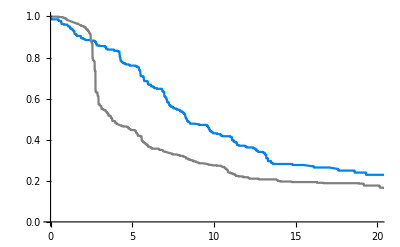

```mathematica
SimulationPlot=Plot[SimulationSurvivalModel[t],{t,0,MaximumTime},PlotRange->{{0,MaximumTime},{0,1}},PlotStyle->Gray,Exclusions->None];

Show[IPDPlot,SimulationPlot]
```

```mathematica
MergedTimes=Join[SimulationEventTimes,IPDdataTimes];
MergedCensoringLabels=Join[SimulationCensoringLabels,IPDdataCensoring];
TreatmentLabels=Join[Table["independence",{Length[SimulationEventTimes]}],Table["observed",{Length[IPDdataTimes]}]];
```

```mathematica
MergedEventData=EventData[MergedTimes,MergedCensoringLabels]
```

EventData[…]

#### loading a Cox Model function

```mathematica
RelativeRiskCalculation[descriptors_,eventdata_,PrintTable_(* set to 1 to print to screen the statistical table of Cox Model output; set to 0 to not show output *)]:=Module[{},
MyModelFit=CoxModelFit[{descriptors,eventdata},{treatment},{treatment},NominalVariables->treatment];

If[PrintTable==1,Print[MyModelFit["ParameterTable"]]];

RelativeRisk=MyModelFit["RelativeRisk"]⟦1⟧;
RelativeRiskLowerConfidenceInterval=MyModelFit["RelativeRiskConfidenceIntervals"]⟦1,1⟧;
RelativeRiskUpperConfidenceInterval=MyModelFit["RelativeRiskConfidenceIntervals"]⟦1,2⟧;

{RelativeRiskLowerConfidenceInterval,RelativeRisk,RelativeRiskUpperConfidenceInterval}
]
```

```mathematica
RelativeRiskCalculation[TreatmentLabels,MergedEventData,1]
```

| Estimate | Standard Error | Relative Risk | Wald-χ^2 | DF | P-Value
treatment[observed] | -0.439566 | 0.069171 | 0.644316 | 40.3831 | 1 | 2.08735×10^-10

{0.562627,0.644316,0.737866}

```mathematica
RelativeRiskCalculation[TreatmentLabels,MergedEventData,1]
```

| Estimate | Standard Error | Relative Risk | Wald-χ^2 | DF | P-Value
treatment[observed] | -0.439566 | 0.069171 | 0.644316 | 40.3831 | 1 | 2.08735×10^-10

{0.562627,0.644316,0.737866}